```mathematica
markers=Import[NotebookDirectory[]<>"output_markers.dat"];
xbeamdm=Import[NotebookDirectory[]<>"output_xbeam_dm.dat"];
xbeamdk=Import[NotebookDirectory[]<>"output_xbeam_dk.dat"]; 
xbeam=Import[NotebookDirectory[]<>"output_xbeam.dat"];
```

```mathematica
plotdm = ListPlot[{ xbeamdm}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Black,Opacity[.5]],FillingStyle->Red, Ticks->Automatic];
plotdk = ListPlot[{ xbeamdk}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Black,Opacity[.5]], FillingStyle->Green, Ticks->Automatic];
plot0 = ListPlot[{ xbeam}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Black,Opacity[.5]],FillingStyle->Red, Ticks->Automatic];
markersplot= ListPlot[{ markers}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->{-30,30}, PlotStyle->RGBColor[.7,.7,.7], Ticks->Automatic];//Quiet
```

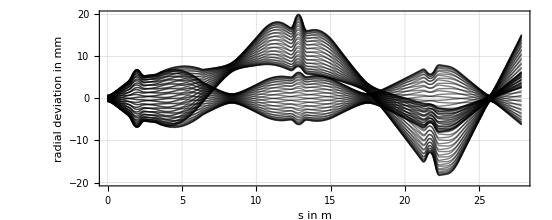

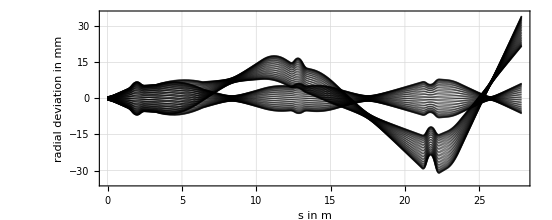

```mathematica
plota = Show[plot0, plotdk, PlotRange->{All,{-20,20}},Frame->True,  FrameLabel->{"s in m","radial deviation in mm"}, FrameTicks->{Automatic,Automatic,{{4.8,"analyzing-MAGNET", {.4,0}, Dashed},{12.83,"ESA - QPT - ESA", {.4,0}, Dashed},{23.5,"switching-MAGNET                      ", {.4,0}, Dashed},{25.7,"           DETECTOR", {.4,0}, Dashed}},{{0,"δ_E= 0 permille"},{8,"δ_E= 3 permille"}}}, GridLines->Automatic, GridLinesStyle->Opacity[.3]]

plotb = Show[plot0, plotdm,PlotRange->{All,{-35,35}},Frame->True,  FrameLabel->{"s in m","radial deviation in mm"}, FrameTicks->{Automatic,Automatic,{{4.8,"analyzing-MAGNET", {.4,0}, Dashed},{12.83,"ESA - QPT - ESA", {.4,0}, Dashed},{23.5,"switching-MAGNET                      ", {.4,0}, Dashed},{25.7,"           DETECTOR", {.4,0}, Dashed}},{{0,"δ_m= 0 permille"},{27,"δ_m= 3 permille"}}}, GridLines->Automatic, GridLinesStyle->Opacity[.3]]
```

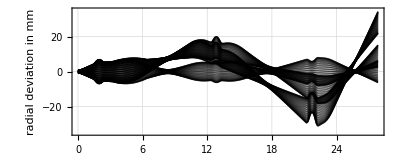

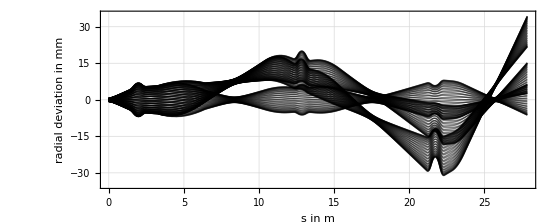

```mathematica
plotc = Show[plot0, plotdk, plotdm, PlotRange->{All,{-35,35}},Frame->True,  FrameLabel->{"s in m","radial deviation in mm"}, FrameTicks->{Automatic,Automatic,{{4.8,"analyzing-MAGNET", {.4,0}, Dashed},{12.83,"ESA - QPT - ESA", {.4,0}, Dashed},           {23.5,"switching-MAGNET                      ", {.4,0}, Dashed},{25.7,"           DETECTOR", {.4,0}, Dashed}},{{0,"δ = 0 permille"},{15,"δ_E= 5 permille"},{45,"δ_m= 5 permille"}}}, GridLines->Automatic, GridLinesStyle->Opacity[.3]]
```

```mathematica
Export[NotebookDirectory[]<>"dk.png", plota, ImageSize->800, ImageResolution->300]
```

G:\GitHub\limioptic\Examples\Mathematica Output\dk.png